### Wprowadzenie wzoru opisującego zależność gęstości powietrza "ρ" od wysokości nad powierzchnią Ziemi "z" ("ρ_o" - gęstość powietrza na powierzchni Ziemi, "μ" - masa molowa powietrza, "g" - przyspieszenie ziemskie, "R" - uniwersalna stała gazowa, "T" - temperatura powietrza).

```mathematica
ClearAll["Global`*"];
```

```mathematica
ρ=ρo×Exp[-(μ×g×z)/(R×T)];
```

### Rozwiązanie równania opisującego zależność współczynnika załamania powietrza na powierzchni Ziemi "n_o" od gęstości powietrza na powierzchni Ziemi "ρ_o", ze względu na "ρ_o".

```mathematica
r1=Solve[no==1+a×ρo, ρo];
```

### Wykorzystanie rozwiązania równania "r_1" do wyprowadzenia wzoru na zależność współczynnika załamania powietrza "n" od współczynnika załamania powietrza na powierzchni Ziemi "n_o", wysokości i temperatury.

```mathematica
n=1+a×ρ/.r1;
```

### Obliczenie czasu (funkcja "τ[h_]") potrzebnego na dotarcie światła w powietrzu na wysokość "h" ("c" - prędkość światła w próżni).

```mathematica
τ[h_]=1/c×∫_0^h nⅆz ;
```

### Wprowadzenie wartości dla uniwersalnej stałej gazowej, przyspieszenia ziemskiego, prędkości światła w próżni, temperatury powietrza, współczynnika załamania powietrza na powierzchni Ziemi i masy molowej powietrza.

```mathematica
R=8.314;       (* J/(mol K) *)
```

```mathematica
g=9.81;          (* m/s^2 *)
```

```mathematica
c=3×10^8;     (* m/s *)
```

```mathematica
T=293;            (* K *)
```

```mathematica
no=1.0003;    (* 1 *)
```

```mathematica
μ=29×10^-3 ;(* kg/mol *)
```

### Obliczenie czasu (funkcja "τ_p[h_]") potrzebnego na dotarcie światła w próżni na wysokość "h".

```mathematica
τp[h_]=h/c;
```

### Obliczenie różnicy (funkcja "Δτ[h_]") czasów "τ[h_]" i "τ_p[h_]".

```mathematica
Δτ[h_]=τ[h]-τp[h];
```

### Sporządzenie wykresu obrazującego zależność różnicy pomiędzy czasem potrzebnym na dotarcie światła w powietrzu i czasem potrzebnym na dotarcie światła w próżni na wysokość "h", od wysokości "h".

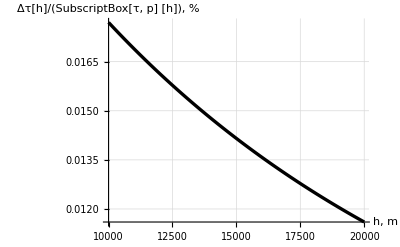

```mathematica
Plot[Δτ[h]/τp[h]×100,{h,10×10^3,20×10^3},
BaseStyle->{FontFamily->"Times",FontSlant->"Italic",FontSize->12},
 PlotStyle->{Black,Thickness[0.006]},
AxesLabel->{" h,  m","Δτ[h]/(SubscriptBox[τ, p] [h]), %"},GridLines->Automatic,GridLinesStyle->Directive[Gray]]
```